```mathematica
originaldata=Import["https://github.com/madsutherland/Project/blob/master/Molecular%20Structures%20Real/Table%20of%20Aouidate%20data.xlsx?raw=true","XLSX"];
```

```mathematica
data1=originaldata[[1]];
```

```mathematica
<<DataImportandNormalization`
```

```mathematica
data2=ReplaceAll[data1,s_String:>ToExpression[s]];(*automate*)
```

```mathematica
data3=deleteZeroRows[data2];
```

```mathematica
data4=deleteZeroColumns[data3];
```

```mathematica
data5=Map[Flatten@{#[[2;;-1]],#[[1]]}&,data4];(*automate*)
{Headers,NumericalData1}={First@data5,Rest@data5};
```

```mathematica
NumericalData1;
```

```mathematica
{dataToNormalize,logMUs}={Most/@NumericalData1,Last/@NumericalData1};
```

```mathematica
dataToNormalize
```

(-82328.7 | 7.374 | -5.682 | 5.522 | -0.16 | 3.242 | 0.046 | -0.707 | 274.154 | 1.54 | 37.9 | 1.324 | 2.455
-30241. | 7.125 | -5.428 | 5.258 | -0.17 | 1.996 | 0.135 | -0.708 | 255.376 | 1.545 | 42.6 | 1.08 | 2.452
-19406.4 | 6.731 | -5.029 | 5.302 | 0.273 | 1.234 | 0.126 | -0.712 | 223.311 | 1.509 | 33.9 | 0.998 | 2.778
-20476.1 | 6.724 | -5.037 | 5.295 | 0.258 | 1.283 | 0.126 | -0.709 | 237.338 | 1.507 | 33.9 | 0.998 | 3.307
-18336.7 | 6.765 | -5.009 | 5.282 | 0.273 | 1.117 | 0.127 | -0.71 | 209.285 | 1.511 | 34.2 | 1.01 | 2.249
-31310.7 | 7.238 | -4.78 | 5.066 | 0.286 | 2.498 | -0.15 | -0.712 | 269.403 | 1.539 | 41.2 | 1.07 | 2.761
-86156.7 | 7.374 | -5.687 | 5.527 | -0.16 | 3.271 | 0.046 | -0.709 | 260.128 | 1.548 | 39.5 | 1.368 | 2.146
-21545.9 | 6.721 | -5.025 | 5.3 | 0.275 | 1.25 | 0.122 | -0.713 | 251.365 | 1.504 | 33.9 | 0.979 | 3.386
-29171.2 | 7.121 | -5.453 | 5.295 | -0.158 | 2.115 | -0.131 | -0.707 | 241.35 | 1.55 | 43.1 | 1.1 | 1.923
-29171. | 6.993 | -5.327 | 5.234 | -0.093 | 4.017 | -0.219 | -0.713 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
-20382.8 | 6.83 | -5.101 | 5.576 | 0.475 | 3.159 | 0.349 | -0.713 | 225.284 | 1.507 | 34.3 | 1.048 | 1.392
-18336.6 | 6.802 | -5.024 | 5.301 | 0.278 | 1.323 | 0.125 | -0.716 | 209.285 | 1.514 | 34.9 | 1.012 | 2.469
-30240.9 | 7.156 | -5.333 | 5.236 | -0.097 | 4.084 | -0.22 | -0.707 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
-17266.8 | 8.353 | -5.142 | 5.451 | 0.309 | 1.618 | 0.133 | -0.714 | 195.258 | 1.516 | 35.3 | 1.026 | 1.94
-22396.4 | 7.075 | -5.349 | 5.755 | 0.407 | 1.297 | 0.273 | -0.713 | 239.268 | 1.54 | 43.5 | 1.184 | 1.644
-21452.6 | 6.803 | -5.073 | 5.531 | 0.458 | 3.234 | 0.353 | -0.707 | 239.311 | 1.504 | 34.3 | 1.034 | 1.921
-28101.4 | 7.292 | -5.423 | 5.335 | -0.088 | 4.378 | -0.223 | -0.708 | 227.323 | 1.559 | 45. | 1.12 | 1.214
-19280.5 | 7.265 | -5.393 | 5.876 | 0.483 | 1.539 | 0.326 | -0.707 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-21452.6 | 7.265 | -5.505 | 5.911 | 0.406 | 3.041 | 0.265 | -0.713 | 239.311 | 1.504 | 34.3 | 1.034 | 1.571
-19280.5 | 6.803 | -4.968 | 5.226 | 0.258 | 1.505 | 0.326 | -0.715 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-22522.4 | 6.911 | -5.063 | 5.528 | 0.465 | 3.276 | 0.352 | -0.713 | 253.337 | 1.502 | 34.2 | 1.022 | 2.45
-20382.8 | 7.265 | -5.505 | 5.908 | 0.403 | 3.089 | 0.225 | -0.714 | 225.284 | 1.508 | 35.2 | 1.05 | 1.262
-23498.6 | 7.374 | -5.703 | 5.961 | 0.257 | 1.288 | 0.269 | -0.714 | 255.31 | 1.503 | 34. | 1.069 | 0.637
-21452.5 | 7.183 | -5.443 | 5.831 | 0.389 | 2.994 | 0.264 | -0.714 | 239.311 | 1.506 | 35.1 | 1.036 | -1.842
-29171. | 7.129 | -5.499 | 5.468 | -0.03 | 3.92 | 0.293 | -0.712 | 241.35 | 1.552 | 44.2 | 1.1 | 1.248
-29171. | 7.102 | -5.569 | 5.499 | -0.07 | 3.714 | 0.289 | -0.708 | 241.35 | 1.552 | 44.2 | 1.1 | -1.003
-28101.4 | 7.319 | -5.536 | 5.488 | -0.049 | 4.009 | 0.293 | -0.702 | 227.323 | 1.559 | 45. | 1.12 | 0.719
-22396.4 | 7.02 | -5.281 | 5.594 | 0.313 | 0.427 | 0.283 | -0.702 | 239.268 | 1.54 | 43.5 | 1.184 | 1.294
-29171. | 7.047 | -5.407 | 5.332 | -0.075 | 4.42 | -0.226 | -0.705 | 241.35 | 1.552 | 44.2 | 1.1 | 1.743
-30240.9 | 7.02 | -5.303 | 5.221 | -0.082 | 4.043 | -0.222 | -0.713 | 255.376 | 1.547 | 43.6 | 1.09 | 2.272
-17266.9 | 7.047 | -5.243 | 5.765 | 0.522 | 2.553 | 0.378 | -0.713 | 195.258 | 1.512 | 34.7 | 1.023 | -1.265
-12104.5 | 7.809 | -5.971 | 6.34 | 0.37 | 1.567 | 0.179 | -0.707 | 149.233 | 1.525 | 35.2 | 0.938 | 2.241
-31310.5 | 7.02 | -5.311 | 5.224 | -0.088 | 4.067 | -0.219 | -0.712 | 269.403 | 1.543 | 43.1 | 1.07 | 2.801
-26669.7 | 7.238 | -5.59 | 5.669 | 0.079 | 3.375 | 0.267 | -0.712 | 301.38 | 1.555 | 39.8 | 1.093 | 2.81
-19280.5 | 7.211 | -5.328 | 5.872 | 0.544 | 1.369 | 0.265 | -0.713 | 209.242 | 1.55 | 45.4 | 1.175 | 1.699
-16164.5 | 7.211 | -5.293 | 5.602 | 0.309 | 1.899 | 0.329 | -0.708 | 179.216 | 1.564 | 48. | 1.163 | 1.707
-22522.2 | 7.156 | -5.435 | 5.827 | 0.391 | 2.947 | 0.265 | -0.713 | 253.337 | 1.503 | 35. | 1.023 | 1.777
-30240.9 | 7.02 | -5.247 | 5.533 | 0.286 | 3.05 | 0.3 | -0.711 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
-30240.9 | 7.156 | -5.533 | 5.466 | -0.067 | 3.751 | 0.285 | -0.71 | 255.376 | 1.547 | 43.6 | 1.09 | 1.777
-20382.8 | 7.319 | -5.524 | 5.912 | 0.388 | 3.136 | 0.245 | -0.719 | 225.284 | 1.507 | 34.3 | 1.048 | 1.042
-21452.6 | 7.129 | -5.41 | 5.794 | 0.384 | 2.979 | 0.26 | -0.713 | 239.311 | 1.506 | 35.1 | 1.036 | 1.273
-20382.7 | 7.238 | -5.481 | 5.872 | 0.39 | 3.237 | 0.249 | -0.713 | 225.284 | 1.508 | 35.2 | 1.05 | 0.744
-19312.9 | 7.319 | -5.523 | 5.914 | 0.391 | 3.203 | 0.253 | -0.707 | 211.258 | 1.511 | 35.4 | 1.067 | 0.215
-19312.8 | 7.456 | -5.719 | 6.007 | 0.288 | 1.449 | 0.305 | -0.71 | 211.258 | 1.511 | 35.4 | 1.067 | -3.08
-17266.8 | 7.292 | -5.444 | 5.849 | 0.405 | 3.673 | 0.308 | -0.717 | 195.258 | 1.512 | 34.7 | 1.023 | 0.435
-16196.9 | 7.292 | -5.443 | 5.848 | 0.406 | 3.724 | 0.307 | -0.713 | 181.232 | 1.517 | 36. | 1.041 | 0.126)

```mathematica
logMUs
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,0.,-0.03,-0.06,-0.67}

```mathematica
logMUsfinal=Drop[logMUs,{43}]
```

{2.72,1.96,2.02,1.95,1.9,1.71,1.69,1.68,1.66,1.36,1.33,1.25,1.29,1.27,1.14,1.36,1.11,1.,1.05,1.,1.38,0.87,0.86,0.83,0.84,0.84,0.81,0.76,0.66,0.68,0.67,0.59,0.58,0.46,0.43,0.41,0.38,0.38,0.38,0.33,0.23,0.03,-0.03,-0.06,-0.67}

```mathematica
Dimensions[logMUsfinal]
```

{45}

```mathematica
rationormalize[list_,pos_:43]:=list/list⟦pos⟧
```

```mathematica
ClearAttributes[rationormalize,Listable]
```

```mathematica
Transpose[dataToNormalize]
```

(-82328.7 | -30241. | -19406.4 | -20476.1 | -18336.7 | -31310.7 | -86156.7 | -21545.9 | -29171.2 | -29171. | -20382.8 | -18336.6 | -30240.9 | -17266.8 | -22396.4 | -21452.6 | -28101.4 | -19280.5 | -21452.6 | -19280.5 | -22522.4 | -20382.8 | -23498.6 | -21452.5 | -29171. | -29171. | -28101.4 | -22396.4 | -29171. | -30240.9 | -17266.9 | -12104.5 | -31310.5 | -26669.7 | -19280.5 | -16164.5 | -22522.2 | -30240.9 | -30240.9 | -20382.8 | -21452.6 | -20382.7 | -19312.9 | -19312.8 | -17266.8 | -16196.9
7.374 | 7.125 | 6.731 | 6.724 | 6.765 | 7.238 | 7.374 | 6.721 | 7.121 | 6.993 | 6.83 | 6.802 | 7.156 | 8.353 | 7.075 | 6.803 | 7.292 | 7.265 | 7.265 | 6.803 | 6.911 | 7.265 | 7.374 | 7.183 | 7.129 | 7.102 | 7.319 | 7.02 | 7.047 | 7.02 | 7.047 | 7.809 | 7.02 | 7.238 | 7.211 | 7.211 | 7.156 | 7.02 | 7.156 | 7.319 | 7.129 | 7.238 | 7.319 | 7.456 | 7.292 | 7.292
-5.682 | -5.428 | -5.029 | -5.037 | -5.009 | -4.78 | -5.687 | -5.025 | -5.453 | -5.327 | -5.101 | -5.024 | -5.333 | -5.142 | -5.349 | -5.073 | -5.423 | -5.393 | -5.505 | -4.968 | -5.063 | -5.505 | -5.703 | -5.443 | -5.499 | -5.569 | -5.536 | -5.281 | -5.407 | -5.303 | -5.243 | -5.971 | -5.311 | -5.59 | -5.328 | -5.293 | -5.435 | -5.247 | -5.533 | -5.524 | -5.41 | -5.481 | -5.523 | -5.719 | -5.444 | -5.443
5.522 | 5.258 | 5.302 | 5.295 | 5.282 | 5.066 | 5.527 | 5.3 | 5.295 | 5.234 | 5.576 | 5.301 | 5.236 | 5.451 | 5.755 | 5.531 | 5.335 | 5.876 | 5.911 | 5.226 | 5.528 | 5.908 | 5.961 | 5.831 | 5.468 | 5.499 | 5.488 | 5.594 | 5.332 | 5.221 | 5.765 | 6.34 | 5.224 | 5.669 | 5.872 | 5.602 | 5.827 | 5.533 | 5.466 | 5.912 | 5.794 | 5.872 | 5.914 | 6.007 | 5.849 | 5.848
-0.16 | -0.17 | 0.273 | 0.258 | 0.273 | 0.286 | -0.16 | 0.275 | -0.158 | -0.093 | 0.475 | 0.278 | -0.097 | 0.309 | 0.407 | 0.458 | -0.088 | 0.483 | 0.406 | 0.258 | 0.465 | 0.403 | 0.257 | 0.389 | -0.03 | -0.07 | -0.049 | 0.313 | -0.075 | -0.082 | 0.522 | 0.37 | -0.088 | 0.079 | 0.544 | 0.309 | 0.391 | 0.286 | -0.067 | 0.388 | 0.384 | 0.39 | 0.391 | 0.288 | 0.405 | 0.406
3.242 | 1.996 | 1.234 | 1.283 | 1.117 | 2.498 | 3.271 | 1.25 | 2.115 | 4.017 | 3.159 | 1.323 | 4.084 | 1.618 | 1.297 | 3.234 | 4.378 | 1.539 | 3.041 | 1.505 | 3.276 | 3.089 | 1.288 | 2.994 | 3.92 | 3.714 | 4.009 | 0.427 | 4.42 | 4.043 | 2.553 | 1.567 | 4.067 | 3.375 | 1.369 | 1.899 | 2.947 | 3.05 | 3.751 | 3.136 | 2.979 | 3.237 | 3.203 | 1.449 | 3.673 | 3.724
0.046 | 0.135 | 0.126 | 0.126 | 0.127 | -0.15 | 0.046 | 0.122 | -0.131 | -0.219 | 0.349 | 0.125 | -0.22 | 0.133 | 0.273 | 0.353 | -0.223 | 0.326 | 0.265 | 0.326 | 0.352 | 0.225 | 0.269 | 0.264 | 0.293 | 0.289 | 0.293 | 0.283 | -0.226 | -0.222 | 0.378 | 0.179 | -0.219 | 0.267 | 0.265 | 0.329 | 0.265 | 0.3 | 0.285 | 0.245 | 0.26 | 0.249 | 0.253 | 0.305 | 0.308 | 0.307
-0.707 | -0.708 | -0.712 | -0.709 | -0.71 | -0.712 | -0.709 | -0.713 | -0.707 | -0.713 | -0.713 | -0.716 | -0.707 | -0.714 | -0.713 | -0.707 | -0.708 | -0.707 | -0.713 | -0.715 | -0.713 | -0.714 | -0.714 | -0.714 | -0.712 | -0.708 | -0.702 | -0.702 | -0.705 | -0.713 | -0.713 | -0.707 | -0.712 | -0.712 | -0.713 | -0.708 | -0.713 | -0.711 | -0.71 | -0.719 | -0.713 | -0.713 | -0.707 | -0.71 | -0.717 | -0.713
274.154 | 255.376 | 223.311 | 237.338 | 209.285 | 269.403 | 260.128 | 251.365 | 241.35 | 241.35 | 225.284 | 209.285 | 255.376 | 195.258 | 239.268 | 239.311 | 227.323 | 209.242 | 239.311 | 209.242 | 253.337 | 225.284 | 255.31 | 239.311 | 241.35 | 241.35 | 227.323 | 239.268 | 241.35 | 255.376 | 195.258 | 149.233 | 269.403 | 301.38 | 209.242 | 179.216 | 253.337 | 255.376 | 255.376 | 225.284 | 239.311 | 225.284 | 211.258 | 211.258 | 195.258 | 181.232
1.54 | 1.545 | 1.509 | 1.507 | 1.511 | 1.539 | 1.548 | 1.504 | 1.55 | 1.552 | 1.507 | 1.514 | 1.547 | 1.516 | 1.54 | 1.504 | 1.559 | 1.55 | 1.504 | 1.55 | 1.502 | 1.508 | 1.503 | 1.506 | 1.552 | 1.552 | 1.559 | 1.54 | 1.552 | 1.547 | 1.512 | 1.525 | 1.543 | 1.555 | 1.55 | 1.564 | 1.503 | 1.547 | 1.547 | 1.507 | 1.506 | 1.508 | 1.511 | 1.511 | 1.512 | 1.517
37.9 | 42.6 | 33.9 | 33.9 | 34.2 | 41.2 | 39.5 | 33.9 | 43.1 | 44.2 | 34.3 | 34.9 | 43.6 | 35.3 | 43.5 | 34.3 | 45. | 45.4 | 34.3 | 45.4 | 34.2 | 35.2 | 34. | 35.1 | 44.2 | 44.2 | 45. | 43.5 | 44.2 | 43.6 | 34.7 | 35.2 | 43.1 | 39.8 | 45.4 | 48. | 35. | 43.6 | 43.6 | 34.3 | 35.1 | 35.2 | 35.4 | 35.4 | 34.7 | 36.
1.324 | 1.08 | 0.998 | 0.998 | 1.01 | 1.07 | 1.368 | 0.979 | 1.1 | 1.1 | 1.048 | 1.012 | 1.09 | 1.026 | 1.184 | 1.034 | 1.12 | 1.175 | 1.034 | 1.175 | 1.022 | 1.05 | 1.069 | 1.036 | 1.1 | 1.1 | 1.12 | 1.184 | 1.1 | 1.09 | 1.023 | 0.938 | 1.07 | 1.093 | 1.175 | 1.163 | 1.023 | 1.09 | 1.09 | 1.048 | 1.036 | 1.05 | 1.067 | 1.067 | 1.023 | 1.041
2.455 | 2.452 | 2.778 | 3.307 | 2.249 | 2.761 | 2.146 | 3.386 | 1.923 | 1.743 | 1.392 | 2.469 | 2.272 | 1.94 | 1.644 | 1.921 | 1.214 | 1.699 | 1.571 | 1.699 | 2.45 | 1.262 | 0.637 | -1.842 | 1.248 | -1.003 | 0.719 | 1.294 | 1.743 | 2.272 | -1.265 | 2.241 | 2.801 | 2.81 | 1.699 | 1.707 | 1.777 | 1.777 | 1.777 | 1.042 | 1.273 | 0.744 | 0.215 | -3.08 | 0.435 | 0.126)

```mathematica
Clear@RatioNormed
```

```mathematica
RatioNormed=Map[rationormalize,Transpose[dataToNormalize]]
```

(4.26288 | 1.56584 | 1.00484 | 1.06023 | 0.949452 | 1.62123 | 4.46109 | 1.11562 | 1.51045 | 1.51044 | 1.0554 | 0.949447 | 1.56584 | 0.894055 | 1.15966 | 1.11079 | 1.45506 | 0.998319 | 1.11079 | 0.998323 | 1.16618 | 1.0554 | 1.21673 | 1.11078 | 1.51044 | 1.51044 | 1.45506 | 1.15966 | 1.51044 | 1.56584 | 0.894061 | 0.626755 | 1.62122 | 1.38093 | 0.998319 | 0.836977 | 1.16617 | 1.56584 | 1.56584 | 1.0554 | 1.11079 | 1.05539 | 1. | 0.999993 | 0.894052 | 0.838658
1.00751 | 0.973494 | 0.919661 | 0.918705 | 0.924307 | 0.988933 | 1.00751 | 0.918295 | 0.972947 | 0.955458 | 0.933188 | 0.929362 | 0.977729 | 1.14128 | 0.966662 | 0.929499 | 0.996311 | 0.992622 | 0.992622 | 0.929499 | 0.944255 | 0.992622 | 1.00751 | 0.981418 | 0.97404 | 0.970351 | 1. | 0.959147 | 0.962836 | 0.959147 | 0.962836 | 1.06695 | 0.959147 | 0.988933 | 0.985244 | 0.985244 | 0.977729 | 0.959147 | 0.977729 | 1. | 0.97404 | 0.988933 | 1. | 1.01872 | 0.996311 | 0.996311
1.02879 | 0.982799 | 0.910556 | 0.912004 | 0.906935 | 0.865472 | 1.02969 | 0.909832 | 0.987326 | 0.964512 | 0.923592 | 0.909651 | 0.965598 | 0.931016 | 0.968495 | 0.918523 | 0.981894 | 0.976462 | 0.996741 | 0.899511 | 0.916712 | 0.996741 | 1.03259 | 0.985515 | 0.995655 | 1.00833 | 1.00235 | 0.956183 | 0.978997 | 0.960167 | 0.949303 | 1.08112 | 0.961615 | 1.01213 | 0.964693 | 0.958356 | 0.984067 | 0.950027 | 1.00181 | 1.00018 | 0.97954 | 0.992395 | 1. | 1.03549 | 0.985696 | 0.985515
0.933717 | 0.889077 | 0.896517 | 0.895333 | 0.893135 | 0.856611 | 0.934562 | 0.896179 | 0.895333 | 0.885019 | 0.942847 | 0.896348 | 0.885357 | 0.921711 | 0.973115 | 0.935238 | 0.902097 | 0.993575 | 0.999493 | 0.883666 | 0.934731 | 0.998985 | 1.00795 | 0.985966 | 0.924586 | 0.929828 | 0.927968 | 0.945891 | 0.901589 | 0.88282 | 0.974806 | 1.07203 | 0.883328 | 0.958573 | 0.992898 | 0.947244 | 0.985289 | 0.935577 | 0.924248 | 0.999662 | 0.979709 | 0.992898 | 1. | 1.01573 | 0.989009 | 0.98884
-0.409207 | -0.434783 | 0.69821 | 0.659847 | 0.69821 | 0.731458 | -0.409207 | 0.703325 | -0.404092 | -0.237852 | 1.21483 | 0.710997 | -0.248082 | 0.790281 | 1.04092 | 1.17136 | -0.225064 | 1.23529 | 1.03836 | 0.659847 | 1.18926 | 1.03069 | 0.657289 | 0.994885 | -0.0767263 | -0.179028 | -0.12532 | 0.800512 | -0.191816 | -0.209719 | 1.33504 | 0.946292 | -0.225064 | 0.202046 | 1.3913 | 0.790281 | 1. | 0.731458 | -0.171355 | 0.992327 | 0.982097 | 0.997442 | 1. | 0.736573 | 1.03581 | 1.03836
1.01218 | 0.623166 | 0.385264 | 0.400562 | 0.348736 | 0.779894 | 1.02123 | 0.390259 | 0.660318 | 1.25414 | 0.986263 | 0.41305 | 1.27505 | 0.505151 | 0.404933 | 1.00968 | 1.36684 | 0.480487 | 0.949422 | 0.469872 | 1.02279 | 0.964408 | 0.402123 | 0.934749 | 1.22385 | 1.15954 | 1.25164 | 0.133313 | 1.37996 | 1.26225 | 0.797065 | 0.489229 | 1.26975 | 1.0537 | 0.427412 | 0.592882 | 0.920075 | 0.952232 | 1.17109 | 0.979082 | 0.930066 | 1.01062 | 1. | 0.452388 | 1.14674 | 1.16266
0.181818 | 0.533597 | 0.498024 | 0.498024 | 0.501976 | -0.592885 | 0.181818 | 0.482213 | -0.517787 | -0.865613 | 1.37945 | 0.494071 | -0.869565 | 0.525692 | 1.07905 | 1.39526 | -0.881423 | 1.28854 | 1.04743 | 1.28854 | 1.3913 | 0.889328 | 1.06324 | 1.04348 | 1.1581 | 1.14229 | 1.1581 | 1.11858 | -0.893281 | -0.87747 | 1.49407 | 0.70751 | -0.865613 | 1.05534 | 1.04743 | 1.3004 | 1.04743 | 1.18577 | 1.12648 | 0.968379 | 1.02767 | 0.98419 | 1. | 1.20553 | 1.21739 | 1.21344
1. | 1.00141 | 1.00707 | 1.00283 | 1.00424 | 1.00707 | 1.00283 | 1.00849 | 1. | 1.00849 | 1.00849 | 1.01273 | 1. | 1.0099 | 1.00849 | 1. | 1.00141 | 1. | 1.00849 | 1.01132 | 1.00849 | 1.0099 | 1.0099 | 1.0099 | 1.00707 | 1.00141 | 0.992928 | 0.992928 | 0.997171 | 1.00849 | 1.00849 | 1. | 1.00707 | 1.00707 | 1.00849 | 1.00141 | 1.00849 | 1.00566 | 1.00424 | 1.01697 | 1.00849 | 1.00849 | 1. | 1.00424 | 1.01414 | 1.00849
1.29772 | 1.20883 | 1.05705 | 1.12345 | 0.990661 | 1.27523 | 1.23133 | 1.18985 | 1.14244 | 1.14244 | 1.06639 | 0.990661 | 1.20883 | 0.924263 | 1.13259 | 1.13279 | 1.07604 | 0.990457 | 1.13279 | 0.990457 | 1.19918 | 1.06639 | 1.20852 | 1.13279 | 1.14244 | 1.14244 | 1.07604 | 1.13259 | 1.14244 | 1.20883 | 0.924263 | 0.706402 | 1.27523 | 1.4266 | 0.990457 | 0.848328 | 1.19918 | 1.20883 | 1.20883 | 1.06639 | 1.13279 | 1.06639 | 1. | 1. | 0.924263 | 0.85787
1.01919 | 1.0225 | 0.998676 | 0.997353 | 1. | 1.01853 | 1.02449 | 0.995367 | 1.02581 | 1.02713 | 0.997353 | 1.00199 | 1.02383 | 1.00331 | 1.01919 | 0.995367 | 1.03177 | 1.02581 | 0.995367 | 1.02581 | 0.994044 | 0.998015 | 0.994705 | 0.996691 | 1.02713 | 1.02713 | 1.03177 | 1.01919 | 1.02713 | 1.02383 | 1.00066 | 1.00927 | 1.02118 | 1.02912 | 1.02581 | 1.03508 | 0.994705 | 1.02383 | 1.02383 | 0.997353 | 0.996691 | 0.998015 | 1. | 1. | 1.00066 | 1.00397
1.07062 | 1.20339 | 0.957627 | 0.957627 | 0.966102 | 1.16384 | 1.11582 | 0.957627 | 1.21751 | 1.24859 | 0.968927 | 0.985876 | 1.23164 | 0.997175 | 1.22881 | 0.968927 | 1.27119 | 1.28249 | 0.968927 | 1.28249 | 0.966102 | 0.99435 | 0.960452 | 0.991525 | 1.24859 | 1.24859 | 1.27119 | 1.22881 | 1.24859 | 1.23164 | 0.980226 | 0.99435 | 1.21751 | 1.12429 | 1.28249 | 1.35593 | 0.988701 | 1.23164 | 1.23164 | 0.968927 | 0.991525 | 0.99435 | 1. | 1. | 0.980226 | 1.01695
1.24086 | 1.01218 | 0.935333 | 0.935333 | 0.946579 | 1.00281 | 1.2821 | 0.917526 | 1.03093 | 1.03093 | 0.982193 | 0.948454 | 1.02156 | 0.961575 | 1.10965 | 0.969072 | 1.04967 | 1.10122 | 0.969072 | 1.10122 | 0.957826 | 0.984067 | 1.00187 | 0.970947 | 1.03093 | 1.03093 | 1.04967 | 1.10965 | 1.03093 | 1.02156 | 0.958763 | 0.8791 | 1.00281 | 1.02437 | 1.10122 | 1.08997 | 0.958763 | 1.02156 | 1.02156 | 0.982193 | 0.970947 | 0.984067 | 1. | 1. | 0.958763 | 0.975633
11.4186 | 11.4047 | 12.9209 | 15.3814 | 10.4605 | 12.8419 | 9.9814 | 15.7488 | 8.94419 | 8.10698 | 6.47442 | 11.4837 | 10.5674 | 9.02326 | 7.64651 | 8.93488 | 5.64651 | 7.90233 | 7.30698 | 7.90233 | 11.3953 | 5.86977 | 2.96279 | -8.56744 | 5.80465 | -4.66512 | 3.34419 | 6.0186 | 8.10698 | 10.5674 | -5.88372 | 10.4233 | 13.0279 | 13.0698 | 7.90233 | 7.93953 | 8.26512 | 8.26512 | 8.26512 | 4.84651 | 5.92093 | 3.46047 | 1. | -14.3256 | 2.02326 | 0.586047)

```mathematica
logNormed=logNormalize[RatioNormed,15]
```

(2.95818 | 2.80734 | 2.77289 | 2.77635 | 2.76942 | 2.81068 | 2.96842 | 2.77979 | 2.80399 | 2.80399 | 2.77605 | 2.76942 | 2.80734 | 2.76595 | 2.78252 | 2.77949 | 2.80063 | 2.77248 | 2.77949 | 2.77248 | 2.78292 | 2.77605 | 2.78604 | 2.77949 | 2.80399 | 2.80399 | 2.80063 | 2.78252 | 2.80399 | 2.80734 | 2.76595 | 2.74898 | 2.81068 | 2.79612 | 2.77248 | 2.76235 | 2.78292 | 2.80734 | 2.80734 | 2.77604 | 2.77949 | 2.77604 | 2.77259 | 2.77259 | 2.76594 | 2.76245
2.77306 | 2.77093 | 2.76755 | 2.76749 | 2.76785 | 2.7719 | 2.77306 | 2.76747 | 2.7709 | 2.7698 | 2.7684 | 2.76816 | 2.7712 | 2.78138 | 2.7705 | 2.76817 | 2.77236 | 2.77213 | 2.77213 | 2.76817 | 2.7691 | 2.77213 | 2.77306 | 2.77143 | 2.77096 | 2.77073 | 2.77259 | 2.77003 | 2.77026 | 2.77003 | 2.77026 | 2.77676 | 2.77003 | 2.7719 | 2.77167 | 2.77167 | 2.7712 | 2.77003 | 2.7712 | 2.77259 | 2.77096 | 2.7719 | 2.77259 | 2.77376 | 2.77236 | 2.77236
2.77439 | 2.77151 | 2.76698 | 2.76707 | 2.76676 | 2.76415 | 2.77444 | 2.76694 | 2.7718 | 2.77037 | 2.7678 | 2.76693 | 2.77044 | 2.76827 | 2.77062 | 2.76748 | 2.77146 | 2.77112 | 2.77239 | 2.76629 | 2.76737 | 2.77239 | 2.77462 | 2.77168 | 2.77232 | 2.77311 | 2.77274 | 2.76985 | 2.77128 | 2.7701 | 2.76942 | 2.77765 | 2.77019 | 2.77335 | 2.77038 | 2.76998 | 2.77159 | 2.76946 | 2.7727 | 2.7726 | 2.77131 | 2.77211 | 2.77259 | 2.7748 | 2.77169 | 2.77168
2.76844 | 2.76563 | 2.7661 | 2.76603 | 2.76589 | 2.76359 | 2.76849 | 2.76608 | 2.76603 | 2.76538 | 2.76901 | 2.76609 | 2.7654 | 2.76768 | 2.77091 | 2.76853 | 2.76645 | 2.77219 | 2.77256 | 2.76529 | 2.7685 | 2.77253 | 2.77309 | 2.77171 | 2.76786 | 2.76819 | 2.76808 | 2.7692 | 2.76642 | 2.76524 | 2.77101 | 2.77708 | 2.76527 | 2.77 | 2.77214 | 2.76929 | 2.77167 | 2.76855 | 2.76784 | 2.77257 | 2.77132 | 2.77214 | 2.77259 | 2.77357 | 2.7719 | 2.77189
2.68039 | 2.67864 | 2.75355 | 2.7511 | 2.75355 | 2.75566 | 2.68039 | 2.75387 | 2.68074 | 2.69207 | 2.78593 | 2.75436 | 2.69137 | 2.75939 | 2.77514 | 2.78324 | 2.69293 | 2.78719 | 2.77498 | 2.7511 | 2.78435 | 2.77451 | 2.75094 | 2.77227 | 2.70292 | 2.69604 | 2.69966 | 2.76004 | 2.69518 | 2.69397 | 2.79331 | 2.76923 | 2.69293 | 2.72143 | 2.79675 | 2.75939 | 2.77259 | 2.75566 | 2.69656 | 2.77211 | 2.77147 | 2.77243 | 2.77259 | 2.75599 | 2.77482 | 2.77498
2.77335 | 2.74875 | 2.73341 | 2.7344 | 2.73103 | 2.75874 | 2.77391 | 2.73373 | 2.75113 | 2.78835 | 2.77173 | 2.73521 | 2.78963 | 2.74117 | 2.73469 | 2.77319 | 2.79526 | 2.73958 | 2.76942 | 2.73889 | 2.77401 | 2.77036 | 2.73451 | 2.7685 | 2.78648 | 2.78251 | 2.78819 | 2.7169 | 2.79606 | 2.78885 | 2.75982 | 2.74014 | 2.78931 | 2.77594 | 2.73615 | 2.74681 | 2.76758 | 2.7696 | 2.78323 | 2.77128 | 2.76821 | 2.77325 | 2.77259 | 2.73776 | 2.78172 | 2.7827
2.7201 | 2.74301 | 2.74071 | 2.74071 | 2.74097 | 2.66772 | 2.7201 | 2.73969 | 2.67292 | 2.64861 | 2.79603 | 2.74046 | 2.64833 | 2.7425 | 2.77752 | 2.79699 | 2.64749 | 2.79046 | 2.77555 | 2.79046 | 2.79675 | 2.76565 | 2.77653 | 2.7753 | 2.78242 | 2.78144 | 2.78242 | 2.77997 | 2.64665 | 2.64777 | 2.803 | 2.75414 | 2.64861 | 2.77604 | 2.77555 | 2.79119 | 2.77555 | 2.78413 | 2.78046 | 2.77061 | 2.77432 | 2.7716 | 2.77259 | 2.78535 | 2.78608 | 2.78584
2.77259 | 2.77268 | 2.77303 | 2.77277 | 2.77285 | 2.77303 | 2.77277 | 2.77312 | 2.77259 | 2.77312 | 2.77312 | 2.77338 | 2.77259 | 2.77321 | 2.77312 | 2.77259 | 2.77268 | 2.77259 | 2.77312 | 2.7733 | 2.77312 | 2.77321 | 2.77321 | 2.77321 | 2.77303 | 2.77268 | 2.77215 | 2.77215 | 2.77241 | 2.77312 | 2.77312 | 2.77259 | 2.77303 | 2.77303 | 2.77312 | 2.77268 | 2.77312 | 2.77294 | 2.77285 | 2.77365 | 2.77312 | 2.77312 | 2.77259 | 2.77285 | 2.77347 | 2.77312
2.79103 | 2.78556 | 2.77615 | 2.78027 | 2.772 | 2.78964 | 2.78694 | 2.78438 | 2.78145 | 2.78145 | 2.77673 | 2.772 | 2.78556 | 2.76784 | 2.78084 | 2.78085 | 2.77733 | 2.77199 | 2.78085 | 2.77199 | 2.78496 | 2.77673 | 2.78554 | 2.78085 | 2.78145 | 2.78145 | 2.77733 | 2.78084 | 2.78145 | 2.78556 | 2.76784 | 2.75407 | 2.78964 | 2.7989 | 2.77199 | 2.76306 | 2.78496 | 2.78556 | 2.78556 | 2.77673 | 2.78085 | 2.77673 | 2.77259 | 2.77259 | 2.76784 | 2.76367
2.77379 | 2.77399 | 2.77251 | 2.77242 | 2.77259 | 2.77375 | 2.77412 | 2.7723 | 2.7742 | 2.77428 | 2.77242 | 2.77271 | 2.77408 | 2.7728 | 2.77379 | 2.7723 | 2.77457 | 2.7742 | 2.7723 | 2.7742 | 2.77222 | 2.77246 | 2.77226 | 2.77238 | 2.77428 | 2.77428 | 2.77457 | 2.77379 | 2.77428 | 2.77408 | 2.77263 | 2.77317 | 2.77391 | 2.77441 | 2.7742 | 2.77478 | 2.77226 | 2.77408 | 2.77408 | 2.77242 | 2.77238 | 2.77246 | 2.77259 | 2.77259 | 2.77263 | 2.77284
2.77699 | 2.78522 | 2.76994 | 2.76994 | 2.77047 | 2.78278 | 2.7798 | 2.76994 | 2.78609 | 2.78801 | 2.77064 | 2.77171 | 2.78696 | 2.77241 | 2.78679 | 2.77064 | 2.7894 | 2.79009 | 2.77064 | 2.79009 | 2.77047 | 2.77224 | 2.77011 | 2.77206 | 2.78801 | 2.78801 | 2.7894 | 2.78679 | 2.78801 | 2.78696 | 2.77135 | 2.77224 | 2.78609 | 2.78033 | 2.79009 | 2.79459 | 2.77188 | 2.78696 | 2.78696 | 2.77064 | 2.77206 | 2.77224 | 2.77259 | 2.77259 | 2.77135 | 2.77365
2.78753 | 2.77335 | 2.76854 | 2.76854 | 2.76924 | 2.77276 | 2.79007 | 2.76742 | 2.77452 | 2.77452 | 2.77148 | 2.76936 | 2.77394 | 2.77018 | 2.77942 | 2.77065 | 2.77569 | 2.77889 | 2.77065 | 2.77889 | 2.76995 | 2.77159 | 2.77271 | 2.77077 | 2.77452 | 2.77452 | 2.77569 | 2.77942 | 2.77452 | 2.77394 | 2.77001 | 2.765 | 2.77276 | 2.77411 | 2.77889 | 2.7782 | 2.77001 | 2.77394 | 2.77394 | 2.77148 | 2.77077 | 2.77159 | 2.77259 | 2.77259 | 2.77001 | 2.77106
3.27407 | 3.27354 | 3.32938 | 3.41383 | 3.23713 | 3.32654 | 3.21813 | 3.42585 | 3.17573 | 3.14013 | 3.06686 | 3.27653 | 3.24132 | 3.17902 | 3.12001 | 3.17534 | 3.02755 | 3.13124 | 3.1049 | 3.13124 | 3.27319 | 3.0383 | 2.8883 | 1.86137 | 3.03518 | 2.33552 | 2.90931 | 3.04541 | 3.14013 | 3.24132 | 2.21006 | 3.23566 | 3.3332 | 3.33469 | 3.13124 | 3.13286 | 3.14696 | 3.14696 | 3.14696 | 2.98803 | 3.04075 | 2.91563 | 2.77259 | -0.393904 | 2.83458 | 2.74638)

```mathematica
input=Drop[logNormed,{-4}]
```

(2.95818 | 2.80734 | 2.77289 | 2.77635 | 2.76942 | 2.81068 | 2.96842 | 2.77979 | 2.80399 | 2.80399 | 2.77605 | 2.76942 | 2.80734 | 2.76595 | 2.78252 | 2.77949 | 2.80063 | 2.77248 | 2.77949 | 2.77248 | 2.78292 | 2.77605 | 2.78604 | 2.77949 | 2.80399 | 2.80399 | 2.80063 | 2.78252 | 2.80399 | 2.80734 | 2.76595 | 2.74898 | 2.81068 | 2.79612 | 2.77248 | 2.76235 | 2.78292 | 2.80734 | 2.80734 | 2.77604 | 2.77949 | 2.77604 | 2.77259 | 2.77259 | 2.76594 | 2.76245
2.77306 | 2.77093 | 2.76755 | 2.76749 | 2.76785 | 2.7719 | 2.77306 | 2.76747 | 2.7709 | 2.7698 | 2.7684 | 2.76816 | 2.7712 | 2.78138 | 2.7705 | 2.76817 | 2.77236 | 2.77213 | 2.77213 | 2.76817 | 2.7691 | 2.77213 | 2.77306 | 2.77143 | 2.77096 | 2.77073 | 2.77259 | 2.77003 | 2.77026 | 2.77003 | 2.77026 | 2.77676 | 2.77003 | 2.7719 | 2.77167 | 2.77167 | 2.7712 | 2.77003 | 2.7712 | 2.77259 | 2.77096 | 2.7719 | 2.77259 | 2.77376 | 2.77236 | 2.77236
2.77439 | 2.77151 | 2.76698 | 2.76707 | 2.76676 | 2.76415 | 2.77444 | 2.76694 | 2.7718 | 2.77037 | 2.7678 | 2.76693 | 2.77044 | 2.76827 | 2.77062 | 2.76748 | 2.77146 | 2.77112 | 2.77239 | 2.76629 | 2.76737 | 2.77239 | 2.77462 | 2.77168 | 2.77232 | 2.77311 | 2.77274 | 2.76985 | 2.77128 | 2.7701 | 2.76942 | 2.77765 | 2.77019 | 2.77335 | 2.77038 | 2.76998 | 2.77159 | 2.76946 | 2.7727 | 2.7726 | 2.77131 | 2.77211 | 2.77259 | 2.7748 | 2.77169 | 2.77168
2.76844 | 2.76563 | 2.7661 | 2.76603 | 2.76589 | 2.76359 | 2.76849 | 2.76608 | 2.76603 | 2.76538 | 2.76901 | 2.76609 | 2.7654 | 2.76768 | 2.77091 | 2.76853 | 2.76645 | 2.77219 | 2.77256 | 2.76529 | 2.7685 | 2.77253 | 2.77309 | 2.77171 | 2.76786 | 2.76819 | 2.76808 | 2.7692 | 2.76642 | 2.76524 | 2.77101 | 2.77708 | 2.76527 | 2.77 | 2.77214 | 2.76929 | 2.77167 | 2.76855 | 2.76784 | 2.77257 | 2.77132 | 2.77214 | 2.77259 | 2.77357 | 2.7719 | 2.77189
2.68039 | 2.67864 | 2.75355 | 2.7511 | 2.75355 | 2.75566 | 2.68039 | 2.75387 | 2.68074 | 2.69207 | 2.78593 | 2.75436 | 2.69137 | 2.75939 | 2.77514 | 2.78324 | 2.69293 | 2.78719 | 2.77498 | 2.7511 | 2.78435 | 2.77451 | 2.75094 | 2.77227 | 2.70292 | 2.69604 | 2.69966 | 2.76004 | 2.69518 | 2.69397 | 2.79331 | 2.76923 | 2.69293 | 2.72143 | 2.79675 | 2.75939 | 2.77259 | 2.75566 | 2.69656 | 2.77211 | 2.77147 | 2.77243 | 2.77259 | 2.75599 | 2.77482 | 2.77498
2.77335 | 2.74875 | 2.73341 | 2.7344 | 2.73103 | 2.75874 | 2.77391 | 2.73373 | 2.75113 | 2.78835 | 2.77173 | 2.73521 | 2.78963 | 2.74117 | 2.73469 | 2.77319 | 2.79526 | 2.73958 | 2.76942 | 2.73889 | 2.77401 | 2.77036 | 2.73451 | 2.7685 | 2.78648 | 2.78251 | 2.78819 | 2.7169 | 2.79606 | 2.78885 | 2.75982 | 2.74014 | 2.78931 | 2.77594 | 2.73615 | 2.74681 | 2.76758 | 2.7696 | 2.78323 | 2.77128 | 2.76821 | 2.77325 | 2.77259 | 2.73776 | 2.78172 | 2.7827
2.7201 | 2.74301 | 2.74071 | 2.74071 | 2.74097 | 2.66772 | 2.7201 | 2.73969 | 2.67292 | 2.64861 | 2.79603 | 2.74046 | 2.64833 | 2.7425 | 2.77752 | 2.79699 | 2.64749 | 2.79046 | 2.77555 | 2.79046 | 2.79675 | 2.76565 | 2.77653 | 2.7753 | 2.78242 | 2.78144 | 2.78242 | 2.77997 | 2.64665 | 2.64777 | 2.803 | 2.75414 | 2.64861 | 2.77604 | 2.77555 | 2.79119 | 2.77555 | 2.78413 | 2.78046 | 2.77061 | 2.77432 | 2.7716 | 2.77259 | 2.78535 | 2.78608 | 2.78584
2.77259 | 2.77268 | 2.77303 | 2.77277 | 2.77285 | 2.77303 | 2.77277 | 2.77312 | 2.77259 | 2.77312 | 2.77312 | 2.77338 | 2.77259 | 2.77321 | 2.77312 | 2.77259 | 2.77268 | 2.77259 | 2.77312 | 2.7733 | 2.77312 | 2.77321 | 2.77321 | 2.77321 | 2.77303 | 2.77268 | 2.77215 | 2.77215 | 2.77241 | 2.77312 | 2.77312 | 2.77259 | 2.77303 | 2.77303 | 2.77312 | 2.77268 | 2.77312 | 2.77294 | 2.77285 | 2.77365 | 2.77312 | 2.77312 | 2.77259 | 2.77285 | 2.77347 | 2.77312
2.79103 | 2.78556 | 2.77615 | 2.78027 | 2.772 | 2.78964 | 2.78694 | 2.78438 | 2.78145 | 2.78145 | 2.77673 | 2.772 | 2.78556 | 2.76784 | 2.78084 | 2.78085 | 2.77733 | 2.77199 | 2.78085 | 2.77199 | 2.78496 | 2.77673 | 2.78554 | 2.78085 | 2.78145 | 2.78145 | 2.77733 | 2.78084 | 2.78145 | 2.78556 | 2.76784 | 2.75407 | 2.78964 | 2.7989 | 2.77199 | 2.76306 | 2.78496 | 2.78556 | 2.78556 | 2.77673 | 2.78085 | 2.77673 | 2.77259 | 2.77259 | 2.76784 | 2.76367
2.77699 | 2.78522 | 2.76994 | 2.76994 | 2.77047 | 2.78278 | 2.7798 | 2.76994 | 2.78609 | 2.78801 | 2.77064 | 2.77171 | 2.78696 | 2.77241 | 2.78679 | 2.77064 | 2.7894 | 2.79009 | 2.77064 | 2.79009 | 2.77047 | 2.77224 | 2.77011 | 2.77206 | 2.78801 | 2.78801 | 2.7894 | 2.78679 | 2.78801 | 2.78696 | 2.77135 | 2.77224 | 2.78609 | 2.78033 | 2.79009 | 2.79459 | 2.77188 | 2.78696 | 2.78696 | 2.77064 | 2.77206 | 2.77224 | 2.77259 | 2.77259 | 2.77135 | 2.77365
2.78753 | 2.77335 | 2.76854 | 2.76854 | 2.76924 | 2.77276 | 2.79007 | 2.76742 | 2.77452 | 2.77452 | 2.77148 | 2.76936 | 2.77394 | 2.77018 | 2.77942 | 2.77065 | 2.77569 | 2.77889 | 2.77065 | 2.77889 | 2.76995 | 2.77159 | 2.77271 | 2.77077 | 2.77452 | 2.77452 | 2.77569 | 2.77942 | 2.77452 | 2.77394 | 2.77001 | 2.765 | 2.77276 | 2.77411 | 2.77889 | 2.7782 | 2.77001 | 2.77394 | 2.77394 | 2.77148 | 2.77077 | 2.77159 | 2.77259 | 2.77259 | 2.77001 | 2.77106
3.27407 | 3.27354 | 3.32938 | 3.41383 | 3.23713 | 3.32654 | 3.21813 | 3.42585 | 3.17573 | 3.14013 | 3.06686 | 3.27653 | 3.24132 | 3.17902 | 3.12001 | 3.17534 | 3.02755 | 3.13124 | 3.1049 | 3.13124 | 3.27319 | 3.0383 | 2.8883 | 1.86137 | 3.03518 | 2.33552 | 2.90931 | 3.04541 | 3.14013 | 3.24132 | 2.21006 | 3.23566 | 3.3332 | 3.33469 | 3.13124 | 3.13286 | 3.14696 | 3.14696 | 3.14696 | 2.98803 | 3.04075 | 2.91563 | 2.77259 | -0.393904 | 2.83458 | 2.74638)

```mathematica
Dimensions@input
```

{12,46}

```mathematica
input2=Transpose[input];
```

```mathematica
inputfinal=Drop[input2,{43}];
```

```mathematica
Dimensions[inputfinal]
```

{45,12}

```mathematica
trainingIndices=Sort@RandomSample[Range[45],35]
```

{2,3,5,6,7,8,9,10,11,12,13,15,16,17,18,20,21,22,23,25,26,27,28,29,30,31,32,34,35,36,37,39,40,42,44}

```mathematica
trainingIndices3={2,3,5,6,7,8,9,10,11,12,13,15,16,17,18,20,21,22,23,25,26,27,28,29,30,31,32,34,35,36,37,39,40,42,44}
```

{2,3,5,6,7,8,9,10,11,12,13,15,16,17,18,20,21,22,23,25,26,27,28,29,30,31,32,34,35,36,37,39,40,42,44}

```mathematica
testIndices=Complement[Range[45],trainingIndices3]
```

{1,4,14,19,24,33,38,41,43,45}

```mathematica
trainingData=inputfinal[[trainingIndices3]];
```

```mathematica
Dimensions[trainingData]
```

{35,12}

```mathematica
trainingResults=logMUsfinal[[trainingIndices3]];
```

```mathematica
Dimensions[trainingResults]
```

{35}

```mathematica
Clear@trainingset
```

```mathematica
trainingset3=Thread[trainingData->trainingResults]
```

{{2.80734,2.77093,2.77151,2.76563,2.67864,2.74875,2.74301,2.77268,2.78556,2.78522,2.77335,3.27354}→1.96,{2.77289,2.76755,2.76698,2.7661,2.75355,2.73341,2.74071,2.77303,2.77615,2.76994,2.76854,3.32938}→2.02,{2.76942,2.76785,2.76676,2.76589,2.75355,2.73103,2.74097,2.77285,2.772,2.77047,2.76924,3.23713}→1.9,{2.81068,2.7719,2.76415,2.76359,2.75566,2.75874,2.66772,2.77303,2.78964,2.78278,2.77276,3.32654}→1.71,{2.96842,2.77306,2.77444,2.76849,2.68039,2.77391,2.7201,2.77277,2.78694,2.7798,2.79007,3.21813}→1.69,{2.77979,2.76747,2.76694,2.76608,2.75387,2.73373,2.73969,2.77312,2.78438,2.76994,2.76742,3.42585}→1.68,{2.80399,2.7709,2.7718,2.76603,2.68074,2.75113,2.67292,2.77259,2.78145,2.78609,2.77452,3.17573}→1.66,{2.80399,2.7698,2.77037,2.76538,2.69207,2.78835,2.64861,2.77312,2.78145,2.78801,2.77452,3.14013}→1.36,{2.77605,2.7684,2.7678,2.76901,2.78593,2.77173,2.79603,2.77312,2.77673,2.77064,2.77148,3.06686}→1.33,{2.76942,2.76816,2.76693,2.76609,2.75436,2.73521,2.74046,2.77338,2.772,2.77171,2.76936,3.27653}→1.25,{2.80734,2.7712,2.77044,2.7654,2.69137,2.78963,2.64833,2.77259,2.78556,2.78696,2.77394,3.24132}→1.29,{2.78252,2.7705,2.77062,2.77091,2.77514,2.73469,2.77752,2.77312,2.78084,2.78679,2.77942,3.12001}→1.14,{2.77949,2.76817,2.76748,2.76853,2.78324,2.77319,2.79699,2.77259,2.78085,2.77064,2.77065,3.17534}→1.36,{2.80063,2.77236,2.77146,2.76645,2.69293,2.79526,2.64749,2.77268,2.77733,2.7894,2.77569,3.02755}→1.11,{2.77248,2.77213,2.77112,2.77219,2.78719,2.73958,2.79046,2.77259,2.77199,2.79009,2.77889,3.13124}→1.,{2.77248,2.76817,2.76629,2.76529,2.7511,2.73889,2.79046,2.7733,2.77199,2.79009,2.77889,3.13124}→1.,{2.78292,2.7691,2.76737,2.7685,2.78435,2.77401,2.79675,2.77312,2.78496,2.77047,2.76995,3.27319}→1.38,{2.77605,2.77213,2.77239,2.77253,2.77451,2.77036,2.76565,2.77321,2.77673,2.77224,2.77159,3.0383}→0.87,{2.78604,2.77306,2.77462,2.77309,2.75094,2.73451,2.77653,2.77321,2.78554,2.77011,2.77271,2.8883}→0.86,{2.80399,2.77096,2.77232,2.76786,2.70292,2.78648,2.78242,2.77303,2.78145,2.78801,2.77452,3.03518}→0.84,{2.80399,2.77073,2.77311,2.76819,2.69604,2.78251,2.78144,2.77268,2.78145,2.78801,2.77452,2.33552}→0.84,{2.80063,2.77259,2.77274,2.76808,2.69966,2.78819,2.78242,2.77215,2.77733,2.7894,2.77569,2.90931}→0.81,{2.78252,2.77003,2.76985,2.7692,2.76004,2.7169,2.77997,2.77215,2.78084,2.78679,2.77942,3.04541}→0.76,{2.80399,2.77026,2.77128,2.76642,2.69518,2.79606,2.64665,2.77241,2.78145,2.78801,2.77452,3.14013}→0.66,{2.80734,2.77003,2.7701,2.76524,2.69397,2.78885,2.64777,2.77312,2.78556,2.78696,2.77394,3.24132}→0.68,{2.76595,2.77026,2.76942,2.77101,2.79331,2.75982,2.803,2.77312,2.76784,2.77135,2.77001,2.21006}→0.67,{2.74898,2.77676,2.77765,2.77708,2.76923,2.74014,2.75414,2.77259,2.75407,2.77224,2.765,3.23566}→0.59,{2.79612,2.7719,2.77335,2.77,2.72143,2.77594,2.77604,2.77303,2.7989,2.78033,2.77411,3.33469}→0.46,{2.77248,2.77167,2.77038,2.77214,2.79675,2.73615,2.77555,2.77312,2.77199,2.79009,2.77889,3.13124}→0.43,{2.76235,2.77167,2.76998,2.76929,2.75939,2.74681,2.79119,2.77268,2.76306,2.79459,2.7782,3.13286}→0.41,{2.78292,2.7712,2.77159,2.77167,2.77259,2.76758,2.77555,2.77312,2.78496,2.77188,2.77001,3.14696}→0.38,{2.80734,2.7712,2.7727,2.76784,2.69656,2.78323,2.78046,2.77285,2.78556,2.78696,2.77394,3.14696}→0.38,{2.77604,2.77259,2.7726,2.77257,2.77211,2.77128,2.77061,2.77365,2.77673,2.77064,2.77148,2.98803}→0.33,{2.77604,2.7719,2.77211,2.77214,2.77243,2.77325,2.7716,2.77312,2.77673,2.77224,2.77159,2.91563}→0.03,{2.76594,2.77236,2.77169,2.7719,2.77482,2.78172,2.78608,2.77347,2.76784,2.77135,2.77001,2.83458}→-0.06}

```mathematica
testData=inputfinal[[testIndices]]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77699 | 2.78753 | 3.27407
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.76994 | 2.76854 | 3.41383
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.77241 | 2.77018 | 3.17902
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.77064 | 2.77065 | 3.1049
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77206 | 2.77077 | 1.86137
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.78609 | 2.77276 | 3.3332
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.78696 | 2.77394 | 3.14696
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77206 | 2.77077 | 3.04075
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | -0.393904
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77365 | 2.77106 | 2.74638)

```mathematica
Dimensions[testData]
```

{10,12}

```mathematica
testResults=logMUsfinal[[testIndices]]
```

{2.72,1.95,1.27,1.05,0.83,0.58,0.38,0.23,-0.03,-0.67}

```mathematica
testset=Thread[testData->testResults]
```

{{2.95818,2.77306,2.77439,2.76844,2.68039,2.77335,2.7201,2.77259,2.79103,2.77699,2.78753,3.27407}→2.72,{2.77635,2.76749,2.76707,2.76603,2.7511,2.7344,2.74071,2.77277,2.78027,2.76994,2.76854,3.41383}→1.95,{2.76595,2.78138,2.76827,2.76768,2.75939,2.74117,2.7425,2.77321,2.76784,2.77241,2.77018,3.17902}→1.27,{2.77949,2.77213,2.77239,2.77256,2.77498,2.76942,2.77555,2.77312,2.78085,2.77064,2.77065,3.1049}→1.05,{2.77949,2.77143,2.77168,2.77171,2.77227,2.7685,2.7753,2.77321,2.78085,2.77206,2.77077,1.86137}→0.83,{2.81068,2.77003,2.77019,2.76527,2.69293,2.78931,2.64861,2.77303,2.78964,2.78609,2.77276,3.3332}→0.58,{2.80734,2.77003,2.76946,2.76855,2.75566,2.7696,2.78413,2.77294,2.78556,2.78696,2.77394,3.14696}→0.38,{2.77949,2.77096,2.77131,2.77132,2.77147,2.76821,2.77432,2.77312,2.78085,2.77206,2.77077,3.04075}→0.23,{2.77259,2.77376,2.7748,2.77357,2.75599,2.73776,2.78535,2.77285,2.77259,2.77259,2.77259,-0.393904}→-0.03,{2.76245,2.77236,2.77168,2.77189,2.77498,2.7827,2.78584,2.77312,2.76367,2.77365,2.77106,2.74638}→-0.67}

## Predict

### Random Forest

```mathematica
p1=Predict[trainingset3,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p1,testset]
```

PredictorMeasurementsObject[…]

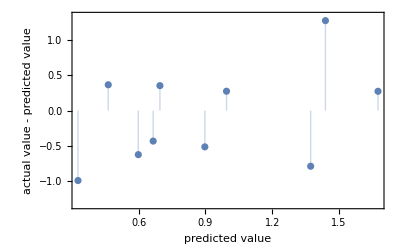
{-Graphics-,0.45254}

```mathematica
pm /@ {"ResidualPlot","MeanSquare"}
```

### Linear Regression

```mathematica
p2=Predict[trainingset,Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
pm2=PredictorMeasurements[p2,testset]
```

PredictorMeasurementsObject[…]

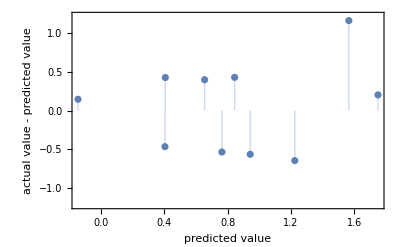
{-Graphics-,0.314391}

```mathematica
pm2/@{"ResidualPlot","MeanSquare"}
```

### Gradient Boosted Trees

```mathematica
p3=Predict[trainingset,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
pm3=PredictorMeasurements[p3,testset]
```

PredictorMeasurementsObject[…]

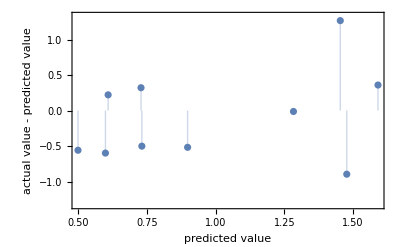
{-Graphics-,0.388239}

```mathematica
pm3/@{"ResidualPlot","MeanSquare"}
```

### Nearest Neighbors

```mathematica
p4=Predict[trainingset,Method->"NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
pm4=PredictorMeasurements[p4,testset]
```

PredictorMeasurementsObject[…]

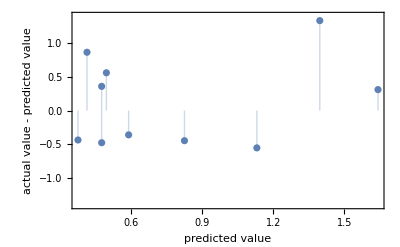
{-Graphics-,0.406071}

```mathematica
pm4/@{"ResidualPlot","MeanSquare"}
```

### Neural Network

```mathematica
p5=Predict[trainingset,Method->"NeuralNetwork"]
```

PredictorFunction[…]

```mathematica
pm5=PredictorMeasurements[p5,testset]
```

PredictorMeasurementsObject[…]

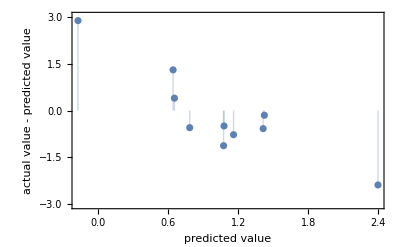
{-Graphics-,1.88158}

```mathematica
pm5/@{"ResidualPlot","MeanSquare"}
```

```mathematica
(*grooooss*)
```

### Gaussian Process

```mathematica
p6=Predict[trainingset,Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
pm6=PredictorMeasurements[p6,testset]
```

PredictorMeasurementsObject[…]

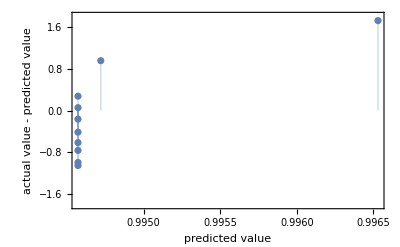
{-Graphics-,0.722436}

```mathematica
pm6/@{"ResidualPlot","MeanSquare"}
```

```mathematica
(*grosss*)
```

### Decision Tree

```mathematica
p7=Predict[trainingset,Method->"DecisionTree"]
```

PredictorFunction[…]

```mathematica
pm7=PredictorMeasurements[p7,testset]
```

PredictorMeasurementsObject[…]

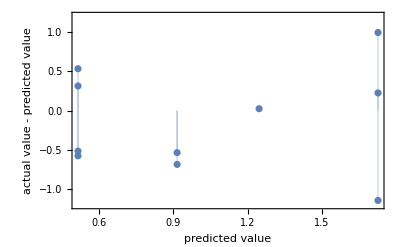
{-Graphics-,0.409317}

```mathematica
pm7/@{"ResidualPlot","MeanSquare"}
```

### From Before

```mathematica
trainingIndices2={1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}
```

{1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}

```mathematica
Dimensions[trainingIndices2]
```

{35}

```mathematica
testIndices2=Complement[Range[45],trainingIndices2]
```

{2,3,7,10,12,21,23,29,36,42}

```mathematica
trainingData2=inputfinal[[trainingIndices2]]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77699 | 2.78753 | 3.27407
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.76994 | 2.76854 | 3.41383
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 2.73103 | 2.74097 | 2.77285 | 2.772 | 2.77047 | 2.76924 | 3.23713
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 2.75874 | 2.66772 | 2.77303 | 2.78964 | 2.78278 | 2.77276 | 3.32654
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 2.73373 | 2.73969 | 2.77312 | 2.78438 | 2.76994 | 2.76742 | 3.42585
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 2.75113 | 2.67292 | 2.77259 | 2.78145 | 2.78609 | 2.77452 | 3.17573
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 2.77173 | 2.79603 | 2.77312 | 2.77673 | 2.77064 | 2.77148 | 3.06686
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 2.78963 | 2.64833 | 2.77259 | 2.78556 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.77241 | 2.77018 | 3.17902
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 2.73469 | 2.77752 | 2.77312 | 2.78084 | 2.78679 | 2.77942 | 3.12001
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 2.77319 | 2.79699 | 2.77259 | 2.78085 | 2.77064 | 2.77065 | 3.17534
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 2.79526 | 2.64749 | 2.77268 | 2.77733 | 2.7894 | 2.77569 | 3.02755
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 2.73958 | 2.79046 | 2.77259 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.77064 | 2.77065 | 3.1049
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 2.73889 | 2.79046 | 2.7733 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 2.77036 | 2.76565 | 2.77321 | 2.77673 | 2.77224 | 2.77159 | 3.0383
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77206 | 2.77077 | 1.86137
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 2.78648 | 2.78242 | 2.77303 | 2.78145 | 2.78801 | 2.77452 | 3.03518
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 2.78251 | 2.78144 | 2.77268 | 2.78145 | 2.78801 | 2.77452 | 2.33552
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 2.78819 | 2.78242 | 2.77215 | 2.77733 | 2.7894 | 2.77569 | 2.90931
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 2.7169 | 2.77997 | 2.77215 | 2.78084 | 2.78679 | 2.77942 | 3.04541
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 2.78885 | 2.64777 | 2.77312 | 2.78556 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 2.75982 | 2.803 | 2.77312 | 2.76784 | 2.77135 | 2.77001 | 2.21006
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 2.74014 | 2.75414 | 2.77259 | 2.75407 | 2.77224 | 2.765 | 3.23566
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.78609 | 2.77276 | 3.3332
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 2.77594 | 2.77604 | 2.77303 | 2.7989 | 2.78033 | 2.77411 | 3.33469
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 2.73615 | 2.77555 | 2.77312 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 2.76758 | 2.77555 | 2.77312 | 2.78496 | 2.77188 | 2.77001 | 3.14696
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.78696 | 2.77394 | 3.14696
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 2.78323 | 2.78046 | 2.77285 | 2.78556 | 2.78696 | 2.77394 | 3.14696
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 2.77128 | 2.77061 | 2.77365 | 2.77673 | 2.77064 | 2.77148 | 2.98803
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77206 | 2.77077 | 3.04075
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | -0.393904
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | 2.78172 | 2.78608 | 2.77347 | 2.76784 | 2.77135 | 2.77001 | 2.83458
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77365 | 2.77106 | 2.74638)

```mathematica
Dimensions[trainingData2]
```

{35,12}

```mathematica
trainingResults2=logMUsfinal[[trainingIndices]];
```

```mathematica
Dimensions[trainingResults2]
```

{35}

```mathematica
trainingset2=Thread[trainingData2->trainingResults2];
```

```mathematica
testData2=inputfinal[[testIndices2]]
```

(2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 2.74875 | 2.74301 | 2.77268 | 2.78556 | 2.78522 | 2.77335 | 3.27354
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.73341 | 2.74071 | 2.77303 | 2.77615 | 2.76994 | 2.76854 | 3.32938
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 2.77391 | 2.7201 | 2.77277 | 2.78694 | 2.7798 | 2.79007 | 3.21813
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 2.78835 | 2.64861 | 2.77312 | 2.78145 | 2.78801 | 2.77452 | 3.14013
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 2.73521 | 2.74046 | 2.77338 | 2.772 | 2.77171 | 2.76936 | 3.27653
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 2.77401 | 2.79675 | 2.77312 | 2.78496 | 2.77047 | 2.76995 | 3.27319
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 2.73451 | 2.77653 | 2.77321 | 2.78554 | 2.77011 | 2.77271 | 2.8883
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 2.79606 | 2.64665 | 2.77241 | 2.78145 | 2.78801 | 2.77452 | 3.14013
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 2.74681 | 2.79119 | 2.77268 | 2.76306 | 2.79459 | 2.7782 | 3.13286
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 2.77325 | 2.7716 | 2.77312 | 2.77673 | 2.77224 | 2.77159 | 2.91563)

```mathematica
Dimensions[testData2]
```

{10,12}

```mathematica
testResults2=logMUsfinal[[testIndices2]]
```

{1.96,2.02,1.69,1.36,1.25,1.38,0.86,0.66,0.41,0.03}

```mathematica
Dimensions[testResults2]
```

{10}

```mathematica
testset2=Thread[testData2->testResults2]
```

{{2.80734,2.77093,2.77151,2.76563,2.67864,2.74875,2.74301,2.77268,2.78556,2.78522,2.77335,3.27354}→1.96,{2.77289,2.76755,2.76698,2.7661,2.75355,2.73341,2.74071,2.77303,2.77615,2.76994,2.76854,3.32938}→2.02,{2.96842,2.77306,2.77444,2.76849,2.68039,2.77391,2.7201,2.77277,2.78694,2.7798,2.79007,3.21813}→1.69,{2.80399,2.7698,2.77037,2.76538,2.69207,2.78835,2.64861,2.77312,2.78145,2.78801,2.77452,3.14013}→1.36,{2.76942,2.76816,2.76693,2.76609,2.75436,2.73521,2.74046,2.77338,2.772,2.77171,2.76936,3.27653}→1.25,{2.78292,2.7691,2.76737,2.7685,2.78435,2.77401,2.79675,2.77312,2.78496,2.77047,2.76995,3.27319}→1.38,{2.78604,2.77306,2.77462,2.77309,2.75094,2.73451,2.77653,2.77321,2.78554,2.77011,2.77271,2.8883}→0.86,{2.80399,2.77026,2.77128,2.76642,2.69518,2.79606,2.64665,2.77241,2.78145,2.78801,2.77452,3.14013}→0.66,{2.76235,2.77167,2.76998,2.76929,2.75939,2.74681,2.79119,2.77268,2.76306,2.79459,2.7782,3.13286}→0.41,{2.77604,2.7719,2.77211,2.77214,2.77243,2.77325,2.7716,2.77312,2.77673,2.77224,2.77159,2.91563}→0.03}

```mathematica
p8=Predict[trainingset2,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pm8=PredictorMeasurements[p8,testset2]
```

PredictorMeasurementsObject[…]

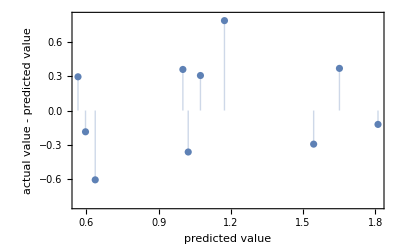
{-Graphics-,0.170006}

```mathematica
pm8/@{"ResidualPlot","MeanSquare"}
```

```mathematica
p9=Predict[trainingset2,Method->{"GradientBoostedTrees"}]
```

PredictorFunction[…]

```mathematica
pm9=PredictorMeasurements[p9,testset2]
```

PredictorMeasurementsObject[…]

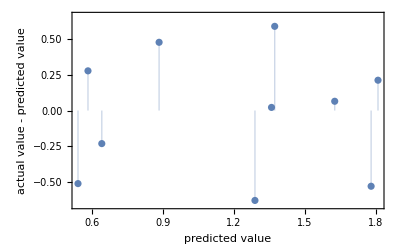
{-Graphics-,0.168852}

```mathematica
pm9/@{"ResidualPlot","MeanSquare"}
```

```mathematica
Sqrt[0.168852]
```

0.410916

```mathematica
(*POSSIBLY BETTER NORMALIZATION FUNCTION TO TEST*)
```

```mathematica
ratioNormalize5[list_,pos_ :4]:=Map[(#/#[[pos]])&,list,-2]
```

```mathematica
ratioNormalize5[{{1,2,5,2},{3,3,9,6}},2]
```

{{1/2,1,5/2,1},{1,1,3,2}}

## FROM BEFORE

```mathematica
trainingIndices2={1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}
```

{1,4,5,6,8,9,11,13,14,15,16,17,18,19,20,22,24,25,26,27,28,30,31,32,33,34,35,37,38,39,40,41,43,44,45}

```mathematica
Dimensions[trainingIndices2]
```

{35}

```mathematica
testIndices2=Complement[Range[45],trainingIndices2]
```

{2,3,7,10,12,21,23,29,36,42}

```mathematica
trainingData2=inputfinal[[trainingIndices2]]
```

(2.95818 | 2.77306 | 2.77439 | 2.76844 | 2.68039 | 2.77335 | 2.7201 | 2.77259 | 2.79103 | 2.77699 | 2.78753 | 3.27407
2.77635 | 2.76749 | 2.76707 | 2.76603 | 2.7511 | 2.7344 | 2.74071 | 2.77277 | 2.78027 | 2.76994 | 2.76854 | 3.41383
2.76942 | 2.76785 | 2.76676 | 2.76589 | 2.75355 | 2.73103 | 2.74097 | 2.77285 | 2.772 | 2.77047 | 2.76924 | 3.23713
2.81068 | 2.7719 | 2.76415 | 2.76359 | 2.75566 | 2.75874 | 2.66772 | 2.77303 | 2.78964 | 2.78278 | 2.77276 | 3.32654
2.77979 | 2.76747 | 2.76694 | 2.76608 | 2.75387 | 2.73373 | 2.73969 | 2.77312 | 2.78438 | 2.76994 | 2.76742 | 3.42585
2.80399 | 2.7709 | 2.7718 | 2.76603 | 2.68074 | 2.75113 | 2.67292 | 2.77259 | 2.78145 | 2.78609 | 2.77452 | 3.17573
2.77605 | 2.7684 | 2.7678 | 2.76901 | 2.78593 | 2.77173 | 2.79603 | 2.77312 | 2.77673 | 2.77064 | 2.77148 | 3.06686
2.80734 | 2.7712 | 2.77044 | 2.7654 | 2.69137 | 2.78963 | 2.64833 | 2.77259 | 2.78556 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.78138 | 2.76827 | 2.76768 | 2.75939 | 2.74117 | 2.7425 | 2.77321 | 2.76784 | 2.77241 | 2.77018 | 3.17902
2.78252 | 2.7705 | 2.77062 | 2.77091 | 2.77514 | 2.73469 | 2.77752 | 2.77312 | 2.78084 | 2.78679 | 2.77942 | 3.12001
2.77949 | 2.76817 | 2.76748 | 2.76853 | 2.78324 | 2.77319 | 2.79699 | 2.77259 | 2.78085 | 2.77064 | 2.77065 | 3.17534
2.80063 | 2.77236 | 2.77146 | 2.76645 | 2.69293 | 2.79526 | 2.64749 | 2.77268 | 2.77733 | 2.7894 | 2.77569 | 3.02755
2.77248 | 2.77213 | 2.77112 | 2.77219 | 2.78719 | 2.73958 | 2.79046 | 2.77259 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.77949 | 2.77213 | 2.77239 | 2.77256 | 2.77498 | 2.76942 | 2.77555 | 2.77312 | 2.78085 | 2.77064 | 2.77065 | 3.1049
2.77248 | 2.76817 | 2.76629 | 2.76529 | 2.7511 | 2.73889 | 2.79046 | 2.7733 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.77605 | 2.77213 | 2.77239 | 2.77253 | 2.77451 | 2.77036 | 2.76565 | 2.77321 | 2.77673 | 2.77224 | 2.77159 | 3.0383
2.77949 | 2.77143 | 2.77168 | 2.77171 | 2.77227 | 2.7685 | 2.7753 | 2.77321 | 2.78085 | 2.77206 | 2.77077 | 1.86137
2.80399 | 2.77096 | 2.77232 | 2.76786 | 2.70292 | 2.78648 | 2.78242 | 2.77303 | 2.78145 | 2.78801 | 2.77452 | 3.03518
2.80399 | 2.77073 | 2.77311 | 2.76819 | 2.69604 | 2.78251 | 2.78144 | 2.77268 | 2.78145 | 2.78801 | 2.77452 | 2.33552
2.80063 | 2.77259 | 2.77274 | 2.76808 | 2.69966 | 2.78819 | 2.78242 | 2.77215 | 2.77733 | 2.7894 | 2.77569 | 2.90931
2.78252 | 2.77003 | 2.76985 | 2.7692 | 2.76004 | 2.7169 | 2.77997 | 2.77215 | 2.78084 | 2.78679 | 2.77942 | 3.04541
2.80734 | 2.77003 | 2.7701 | 2.76524 | 2.69397 | 2.78885 | 2.64777 | 2.77312 | 2.78556 | 2.78696 | 2.77394 | 3.24132
2.76595 | 2.77026 | 2.76942 | 2.77101 | 2.79331 | 2.75982 | 2.803 | 2.77312 | 2.76784 | 2.77135 | 2.77001 | 2.21006
2.74898 | 2.77676 | 2.77765 | 2.77708 | 2.76923 | 2.74014 | 2.75414 | 2.77259 | 2.75407 | 2.77224 | 2.765 | 3.23566
2.81068 | 2.77003 | 2.77019 | 2.76527 | 2.69293 | 2.78931 | 2.64861 | 2.77303 | 2.78964 | 2.78609 | 2.77276 | 3.3332
2.79612 | 2.7719 | 2.77335 | 2.77 | 2.72143 | 2.77594 | 2.77604 | 2.77303 | 2.7989 | 2.78033 | 2.77411 | 3.33469
2.77248 | 2.77167 | 2.77038 | 2.77214 | 2.79675 | 2.73615 | 2.77555 | 2.77312 | 2.77199 | 2.79009 | 2.77889 | 3.13124
2.78292 | 2.7712 | 2.77159 | 2.77167 | 2.77259 | 2.76758 | 2.77555 | 2.77312 | 2.78496 | 2.77188 | 2.77001 | 3.14696
2.80734 | 2.77003 | 2.76946 | 2.76855 | 2.75566 | 2.7696 | 2.78413 | 2.77294 | 2.78556 | 2.78696 | 2.77394 | 3.14696
2.80734 | 2.7712 | 2.7727 | 2.76784 | 2.69656 | 2.78323 | 2.78046 | 2.77285 | 2.78556 | 2.78696 | 2.77394 | 3.14696
2.77604 | 2.77259 | 2.7726 | 2.77257 | 2.77211 | 2.77128 | 2.77061 | 2.77365 | 2.77673 | 2.77064 | 2.77148 | 2.98803
2.77949 | 2.77096 | 2.77131 | 2.77132 | 2.77147 | 2.76821 | 2.77432 | 2.77312 | 2.78085 | 2.77206 | 2.77077 | 3.04075
2.77259 | 2.77376 | 2.7748 | 2.77357 | 2.75599 | 2.73776 | 2.78535 | 2.77285 | 2.77259 | 2.77259 | 2.77259 | -0.393904
2.76594 | 2.77236 | 2.77169 | 2.7719 | 2.77482 | 2.78172 | 2.78608 | 2.77347 | 2.76784 | 2.77135 | 2.77001 | 2.83458
2.76245 | 2.77236 | 2.77168 | 2.77189 | 2.77498 | 2.7827 | 2.78584 | 2.77312 | 2.76367 | 2.77365 | 2.77106 | 2.74638)

```mathematica
Dimensions[trainingData2]
```

{35,12}

```mathematica
trainingResults2=logMUsfinal[[trainingIndices]];
```

```mathematica
Dimensions[trainingResults2]
```

{35}

```mathematica
trainingset2=Thread[trainingData2->trainingResults2];
```

```mathematica
testData2=inputfinal[[testIndices2]]
```

(2.80734 | 2.77093 | 2.77151 | 2.76563 | 2.67864 | 2.74875 | 2.74301 | 2.77268 | 2.78556 | 2.78522 | 2.77335 | 3.27354
2.77289 | 2.76755 | 2.76698 | 2.7661 | 2.75355 | 2.73341 | 2.74071 | 2.77303 | 2.77615 | 2.76994 | 2.76854 | 3.32938
2.96842 | 2.77306 | 2.77444 | 2.76849 | 2.68039 | 2.77391 | 2.7201 | 2.77277 | 2.78694 | 2.7798 | 2.79007 | 3.21813
2.80399 | 2.7698 | 2.77037 | 2.76538 | 2.69207 | 2.78835 | 2.64861 | 2.77312 | 2.78145 | 2.78801 | 2.77452 | 3.14013
2.76942 | 2.76816 | 2.76693 | 2.76609 | 2.75436 | 2.73521 | 2.74046 | 2.77338 | 2.772 | 2.77171 | 2.76936 | 3.27653
2.78292 | 2.7691 | 2.76737 | 2.7685 | 2.78435 | 2.77401 | 2.79675 | 2.77312 | 2.78496 | 2.77047 | 2.76995 | 3.27319
2.78604 | 2.77306 | 2.77462 | 2.77309 | 2.75094 | 2.73451 | 2.77653 | 2.77321 | 2.78554 | 2.77011 | 2.77271 | 2.8883
2.80399 | 2.77026 | 2.77128 | 2.76642 | 2.69518 | 2.79606 | 2.64665 | 2.77241 | 2.78145 | 2.78801 | 2.77452 | 3.14013
2.76235 | 2.77167 | 2.76998 | 2.76929 | 2.75939 | 2.74681 | 2.79119 | 2.77268 | 2.76306 | 2.79459 | 2.7782 | 3.13286
2.77604 | 2.7719 | 2.77211 | 2.77214 | 2.77243 | 2.77325 | 2.7716 | 2.77312 | 2.77673 | 2.77224 | 2.77159 | 2.91563)

```mathematica
Dimensions[testData2]
```

{10,12}

```mathematica
testResults2=logMUsfinal[[testIndices2]]
```

{1.96,2.02,1.69,1.36,1.25,1.38,0.86,0.66,0.41,0.03}

```mathematica
Dimensions[testResults2]
```

{10}

```mathematica
testset2=Thread[testData2->testResults2]
```

{{2.80734,2.77093,2.77151,2.76563,2.67864,2.74875,2.74301,2.77268,2.78556,2.78522,2.77335,3.27354}→1.96,{2.77289,2.76755,2.76698,2.7661,2.75355,2.73341,2.74071,2.77303,2.77615,2.76994,2.76854,3.32938}→2.02,{2.96842,2.77306,2.77444,2.76849,2.68039,2.77391,2.7201,2.77277,2.78694,2.7798,2.79007,3.21813}→1.69,{2.80399,2.7698,2.77037,2.76538,2.69207,2.78835,2.64861,2.77312,2.78145,2.78801,2.77452,3.14013}→1.36,{2.76942,2.76816,2.76693,2.76609,2.75436,2.73521,2.74046,2.77338,2.772,2.77171,2.76936,3.27653}→1.25,{2.78292,2.7691,2.76737,2.7685,2.78435,2.77401,2.79675,2.77312,2.78496,2.77047,2.76995,3.27319}→1.38,{2.78604,2.77306,2.77462,2.77309,2.75094,2.73451,2.77653,2.77321,2.78554,2.77011,2.77271,2.8883}→0.86,{2.80399,2.77026,2.77128,2.76642,2.69518,2.79606,2.64665,2.77241,2.78145,2.78801,2.77452,3.14013}→0.66,{2.76235,2.77167,2.76998,2.76929,2.75939,2.74681,2.79119,2.77268,2.76306,2.79459,2.7782,3.13286}→0.41,{2.77604,2.7719,2.77211,2.77214,2.77243,2.77325,2.7716,2.77312,2.77673,2.77224,2.77159,2.91563}→0.03}

```mathematica
p8=Predict[trainingset2,Method->{"RandomForest","LeafSize"->1,"DistributionSmoothing"->0.3}]
```

PredictorFunction[…]

```mathematica
pm8=PredictorMeasurements[p8,testset2]
```

PredictorMeasurementsObject[…]

```mathematica
pm8/@{"ResidualPlot","MeanSquare"}
```

{-Graphics-,0.170006}

```mathematica
p9=Predict[trainingset2,Method->{"GradientBoostedTrees"}]
```

PredictorFunction[…]

```mathematica
pm9=PredictorMeasurements[p9,testset2]
```

PredictorMeasurementsObject[…]

```mathematica
pm9/@{"ResidualPlot","MeanSquare"}
```

{-Graphics-,0.168852}

```mathematica
Sqrt[0.168852]
```

0.410916

```mathematica
(*POSSIBLY BETTER NORMALIZATION FUNCTION TO TEST*)
```

```mathematica
ratioNormalize5[list_,pos_ :4]:=Map[(#/#[[pos]])&,list,-2]
```

```mathematica
ratioNormalize5[{{1,2,5,2},{3,3,9,6}},2]
```

{{1/2,1,5/2,1},{1,1,3,2}}